-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 14 IV.G Examples

```mathematica
(*-------------------------------------*)
t1=TimeObject[{7,0,0}];
t2=TimeObject[{7,10,0}];
Lab1="Thermo.&Stat.\nGeneral Picture";
(*-------------------------------------*)
(*-------------------------------------*)
t3=TimeObject[{7,8,0}];
t4=TimeObject[{7,30,0}];
Lab2="Thermo.&Stat.\nMindMap Lecture";
(*-------------------------------------*)
(*-------------------------------------*)
t5=TimeObject[{8,2,0}];
t6=TimeObject[{8,20,0}];
Lab3="Thermo.&Stat.\nStudents talks";
(*-------------------------------------*)
(*-------------------------------------*)
t71=TimeObject[{8,5,0}];
t81=TimeObject[{8,10,0}];
Lab41="Thermo.&Stat.\nBreak";
(*-------------------------------------*)
(*-------------------------------------*)
t7=TimeObject[{7,35,0}];
t8=TimeObject[{8,45,0}];
Lab4="Thermo.&Stat.\nSlides";
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
t72=TimeObject[{8,50,0}];
t82=TimeObject[{9,0,0}];
Lab42=Hyperlink[Style["Thermo.&Stat.\n   Questions?\n   &\n   Chat..."],"https://mmaitex-gemmini.fly.dev/"];

TS1=TimelinePlot[{
Interval[{t1,t2}]->Lab1,
Interval[{t3,t4}]->Lab2,
Interval[{t5,t6}]->Lab3,
Interval[{t71,t81}]->Lab41,
Interval[{t7,t8}]->Lab4,
Interval[{t72,t82}]->Lab42
},
Frame->True,
FrameStyle->Directive[Thickness[0.003],FontFamily->"Comic Sans MS", FontSize->28],
LabelStyle->Directive[FontFamily->"Comic Sans MS",Black,18],ImageSize->800,Background->LightBlue,AspectRatio->0.35
]
```

-Graphics-

```mathematica
(1) -- Let's revisit our earlier examples using the canonical ensemble approach. Remember, in this ensemble, we're dealing with a system that can exchange energy with its surroundings but has a fixed number of particles.

For the ideal gas, we can now express its properties in terms of the partition function. This function encapsulates all the possible energy states of the system. From it, we can derive important thermodynamic quantities like the free energy and entropy.

In the case of the paramagnetic system, the canonical ensemble treatment allows us to explore how the system behaves at different temperatures. We can calculate the average magnetic moment and see how it changes as we heat or cool the system.

By using the canonical ensemble, we gain a deeper understanding of these systems' behavior at constant temperature, providing a more realistic model for many practical situations.
```

## Two level systems

```mathematica
(2) -- Let's talk about a simple system with two energy levels. Imagine we have N tiny particles, like impurities in a material. We can describe the overall state of these particles using two pieces of information: the temperature T and the number of particles N. We call this the macro-state M.

Each particle can be in one of two states: a low energy state or a high energy state. The energy difference between these states is ε. We use a mathematical tool called the Hamiltonian to describe the total energy of the system. It looks like this:

H = ε × (sum of all particles in the high energy state)

Now, in this system, each possible arrangement of particles in low and high energy states is called a micro-state μ. The probability of finding the system in a particular micro-state depends on the temperature and follows a special rule in statistical mechanics called the canonical probability distribution.
```

Statistical Mechanics
Ramirez (3)

```mathematica
MaTeX["p\\left(\\left\\{n_{i}\\right\\}\\right)=\\frac{1}{Z} \\exp \\left[-\\beta \\epsilon \\sum_{i=1}^{N} n_{i}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p\\left(\\left\\{n_{i}\\right\\}\\right)=\\frac{1}{Z} \\exp \\left[-\\beta \\epsilon \\sum_{i=1}^{N} n_{i}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[{n_i}]==exp[-βϵ ∑_(i=1)^N n_i]/Z

```mathematica
(4) -- From the partition function,(4)
```

Statistical Mechanics
Ramirez (5)

```mathematica
MaTeX["\\begin{aligned}Z(T, N) & =\\\\ \\sum_{\\left\\{n_{i}\\right\\}} \\exp \\left[-\\beta \\epsilon \\sum_{i=1}^{N} n_{i}\\right]=\\\\ \\left(\\sum_{n_{1}=0}^{1} e^{-\\beta \\epsilon n_{1}}\\right) \\cdots\\left(\\sum_{n_{N}=0}^{1} e^{-\\beta \\epsilon n_{N}}\\right) \\\\& =\\\\ \\left(1+e^{-\\beta \\epsilon}\\right)^{N}\\end{aligned}", Magnification -> 4]
```

-Graphics-

(6) -- In thermodynamics, we're often interested in the free energy of a system. This quantity helps us understand how much useful work we can extract from a process. For a canonical ensemble, we define the Helmholtz free energy as:

F = -kT ln Z

Here, k is Boltzmann's constant, T is temperature, and Z is the partition function. This equation connects the microscopic details of our system (contained in Z) to a macroscopic thermodynamic property (F).

The free energy is particularly useful because it combines both energy and entropy effects. It tells us about the system's tendency to minimize its energy while maximizing its entropy, subject to the constraints of constant temperature and volume.

Understanding free energy is crucial for predicting spontaneous processes and equilibrium states in various physical and chemical systems.

Statistical Mechanics
Ramirez (7)

```mathematica
MaTeX["\\begin{aligned} F(T, N)=-k_{B} T \\ln Z=\\\\ -N k_{B} T \\ln \\left[1+e^{-\\epsilon /\\left(k_{B} T\\right)}\\right] \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["F(T, N)=-k_{B} T \\ln Z=-N k_{B} T \\ln \\left[1+e^{-\\epsilon /\\left(k_{B} T\\right)}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

F[T,N]==-k_B T ln Z==-N k_B T ln[1+e^(-ϵ/(k_B T))]

```mathematica
(8) -- The entropy is now given by
```

Statistical Mechanics
Ramirez (9)

```mathematica
MaTeX["\\begin{aligned} S=-\\left.\\frac{\\partial F}{\\partial T}\\right|_{N}\\\\= \\underbrace{N k_{B} \\ln \\left[1+e^{-\\epsilon /\\left(k_{B} T\\right)}\\right]}_{-F / T}\\\\+N k_{B} T\\left(\\frac{\\epsilon}{k_{B} T^{2}}\\right) \\frac{e^{-\\epsilon /\\left(k_{B} T\\right)}}{1+e^{-\\epsilon /\\left(k_{B} T\\right)}} \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(10) -- The internal energy
```

Statistical Mechanics
Ramirez (11)

```mathematica
MaTeX["E=F+T S=\\frac{N \\epsilon}{1+e^{\\epsilon /\\left(k_{B} T\\right)}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["Ener=F+T S=\\frac{N \\epsilon}{1+e^{\\epsilon /\\left(k_{B} T\\right)}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Ener==F+TS==(N ϵ)/(1+e^(ϵ/(k_B T)))

```mathematica
(12) -- can also be obtained from
```

Statistical Mechanics
Ramirez (13)

```mathematica
MaTeX["E=-\\frac{\\partial \\ln Z}{\\partial \\beta}=\\frac{N \\epsilon e^{-\\beta \\epsilon}}{1+e^{-\\beta \\epsilon}}", Magnification -> 4]
```

-Graphics-

```mathematica
(14) -- Since the joint probability in eq.(IV.71) is in the form of a product, the excitations of different impurities are independent of each other, with the unconditional distribution
```

Statistical Mechanics
Ramirez (15)

```mathematica
MaTeX["p(n)=\\frac{e^{-\\beta \\epsilon n}}{1+e^{-\\beta \\epsilon}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p(n)=\\frac{e^{-\\beta \\epsilon n}}{1+e^{-\\beta \\epsilon}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[n]==e^(-βϵ n)/(1+e^-βϵ)

(16) -- When we study large systems with many particles, we can use different methods to understand their behavior. Two common approaches are the canonical and microcanonical ensembles. 

In our earlier work, we found a result using the microcanonical ensemble, which is equation (IV.25). Now, we've reached the same conclusion using the canonical ensemble.

This isn't surprising! When we look at systems with a very large number of particles (N), both methods give us the same information about how the system behaves. This applies to both the big picture (macroscopic) and the tiny details (microscopic).

So, whether we use the canonical or microcanonical approach, we end up describing the same physics for these large systems.

## The Ideal Gas

```mathematica
For the canonical macro-state $M \equiv(T, V, N)$, the joint $\mathrm{PDF}$ for the micro-states ,
```

```mathematica
MaTeX["\\mu \\equiv \\left\\{\\vec{p}_{i}, \\vec{q}_{i}\\right\\}", Magnification->4]
```

-Graphics-

is

Statistical Mechanics
Ramirez (18)

```mathematica
MaTeX["p\\left(\\left\\{\\vec{p}_{i}, \\vec{q}_{i}\\right\\}\\right)=\\frac{1}{Z} \\exp \\left[-\\beta \\sum_{i=1}^{N} \\frac{p_{i}^{2}}{2 m}\\right] \\cdot \\begin{cases}1 & \\text {for}\\left\\{\\vec{q}_{i}\\right\\} \\in \\text {box} \\\\ 0 & \\text {otherwise}\\end{cases}", Magnification -> 4]
```

-Graphics-

(19) -- Let's consider how we calculate the partition function when we have identical particles. We need to adjust our phase space to account for this. When we do, we end up with a dimensionless partition function. This is important because it helps us understand the behavior of systems with many identical particles, like gases or certain types of materials. By using this approach, we can predict various thermodynamic properties of these systems more accurately.

Statistical Mechanics
Ramirez (20)

```mathematica
MaTeX["\\begin{aligned}Z(T, V, N) & =\\int \\frac{1}{N!} \\prod_{i=1}^{N} \\frac{d^{3} \\vec{q}_{i} d^{3} \\vec{p}_{i}}{h^{3}} \\exp \\left[-\\beta \\sum_{i=1}^{N} \\frac{p_{i}^{2}}{2 m}\\right] \\\\& =\\frac{V^{N}}{N!}\\left(\\frac{2 \\pi m k_{B} T}{h^{2}}\\right)^{3 N / 2}=\\frac{1}{N!}\\left(\\frac{V}{\\lambda(T)^{3}}\\right)^{N}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(21) -- where
```

Statistical Mechanics
Ramirez (22)

```mathematica
MaTeX["\\lambda(T)=\\frac{h}{\\sqrt{2 \\pi m k_{B} T}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\lambda(T)=\\frac{h}{\\sqrt{2 \\pi m k_{B} T}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

λ[T]==h/(√(2 π m k_B T))

(23) -- is a characteristic length associated with the action $h$. It shall be demonstrated later on that this length scale controls the onset of quantum mechanical effects in an ideal gas.

```mathematica
(24) -- The free energy is given by(24) -- In thermodynamics, we define the free energy F as:

F = U - TS

Here, U is the internal energy, T is the temperature, and S is the entropy of the system. This equation helps us understand how energy changes in a system at constant temperature. The free energy tells us how much useful work we can get from a system, taking into account both energy and entropy changes.
```

Statistical Mechanics
Ramirez (25)

```mathematica
MaTeX["\\begin{aligned}F & =-k_{B} T \\ln Z\\\\=-N k_{B} T \\ln V+N k_{B} T \\ln N-N k_{B} T-\\\\\\frac{3 N}{2} k_{B} T \\ln \\left(\\frac{2 \\pi m k_{B} T}{h^{2}}\\right) \\\\& =\\\\-N k_{B} T\\left[\\ln \\left(\\frac{V e}{N}\\right)+\\frac{3}{2} \\ln \\left(\\frac{2 \\pi m k_{B} T}{h^{2}}\\right)\\right]\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(26) -- Let's explore how we can find different properties of an ideal gas using a simple equation. We start with the equation dF = -SdT - PdV + μdN. This equation is like a key that unlocks many doors in thermodynamics. 

For instance, we can use it to find the entropy of the gas. Entropy tells us about the disorder in the system. By looking at how our equation changes when we change the temperature, we can figure out the entropy.

This approach isn't limited to just entropy. We can use the same equation to find other important properties of the ideal gas too. It's a powerful tool that helps us understand how the gas behaves under different conditions.
```

Statistical Mechanics
Ramirez (27)

```mathematica
MaTeX["\\begin{aligned} -S=\\left.\\frac{\\partial F}{\\partial T}\\right|_{V, N}\\\\= -N k_{B}\\left[\\ln \\frac{V e}{N}+\\frac{3}{2} \\ln \\left(\\frac{2 \\pi m k_{B} T}{h^{2}}\\right)\\right]\\\\-N k_{B} T \\frac{3}{2 T}=\\\\ \\frac{F-E}{T} \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(28) -- Let's break down the internal energy of an ideal gas in simple terms. For a system with N particles, each particle has three degrees of freedom in three-dimensional space. This means each particle can move in three different directions. 

The average energy per degree of freedom is kB T/2, where kB is Boltzmann's constant and T is the temperature. Since we have three degrees of freedom per particle, and N particles in total, the internal energy becomes:

E = 3N × (kB T/2) = 3NkB T/2

This equation tells us that the internal energy of an ideal gas depends only on the number of particles and the temperature, not on the volume or pressure. It's a fundamental result in thermodynamics and statistical mechanics.

The equation of state, which relates pressure, volume, and temperature, can be derived from this internal energy expression using statistical mechanics principles.
```

Statistical Mechanics
Ramirez (29)

```mathematica
MaTeX["\\begin{aligned} P=-\\left.\\frac{\\partial F}{\\partial V}\\right|_{T, N}=\\\\ \\frac{N k_{B} T}{V}, \\quad \\Longrightarrow \\quad P V=N k_{B} T \\end{aligned}", Magnification -> 4]
```

-Graphics-

(30) -- and the chemical potential is given by

Statistical Mechanics
Ramirez (31)

```mathematica
MaTeX["\\begin{aligned} \\mu=\\left.\\frac{\\partial F}{\\partial N}\\right|_{T, V}=\\\\ \\frac{F}{N}+k_{B} T=\\\\ \\frac{E-T S+P V}{N}=k_{B} T \\ln \\left(n \\lambda^{3}\\right) \\end{aligned}", Magnification -> 4]
```

-Graphics-

(32) -- Also, according to eq.(IV.78), the momenta of the $N$ particles are taken from independent Maxwell-Boltzmann distributions, consistent with eq.(IV.39).

## IV.H The Gibbs Canonical Ensemble

(33) -- Here's a simplified version of the text, written as if for an undergraduate textbook on Thermodynamics and Statistics:

The Gibbs Canonical Ensemble

We can create a more general canonical ensemble that considers both heat and work when changing the system's internal energy. In this ensemble, we define macrostates M as (T, J), where T is the external temperature and J represents the forces acting on the system. The thermodynamic coordinates x are treated as additional random variables.

External elements, such as pistons or magnets, keep the force constant. The energy of the combined system, including these external elements, is H - J · x. While the work done on the system is +J · x, the energy change for the external elements has the opposite sign.

The microstates in this combined system follow canonical probability distributions. This approach allows us to study systems where both heat transfer and mechanical work are important.

Statistical Mechanics
Ramirez (34)

```mathematica
MaTeX["p\\left(\\mu_{\\mathrm{S}}, \\mathbf{x}\\right)=\\exp \\left[-\\beta \\mathcal{H}\\left(\\mu_{\\mathrm{S}}\\right)+\\beta \\mathbf{J} \\cdot \\mathbf{x}\\right] / \\mathcal{Z}(T, N, \\mathbf{J})", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p\\left(\\mu_{\\mathrm{S}}, \\mathbf{x}\\right)=\\exp \\left[-\\beta \\mathcal{H}\\left(\\mu_{\\mathrm{S}}\\right)+\\beta \\mathbf{J} \\cdot \\mathbf{x}\\right] / \\mathcal{Z}(T, N, \\mathbf{J})",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[μ_S,x]==exp[-β H[μ_S]+β J·x]/Z[T,N,J]

(35) -- with the Gibbs partition function

Statistical Mechanics
Ramirez (36)

```mathematica
MaTeX["\\mathcal{Z}(N, T, \\mathbf{J})=\\sum_{\\mu_{\\mathrm{S}}, \\mathbf{x}} e^{\\beta \\mathbf{J} \\cdot \\mathbf{x}-\\beta \\mathcal{H}\\left(\\mu_{\\mathrm{S}}\\right)}", Magnification -> 4]
```

-Graphics-

```mathematica
(37) -- In our discussion of the Canonical Ensemble, we've included the particle number N in our equations. This is important because it shows that we're not dealing with chemical work in this context. Chemical work involves changes in the number of particles, which we're keeping constant here. We'll explore situations where the particle number can change when we look at the Grand Canonical Ensemble in the next section. For now, remember that N stays fixed in the Canonical Ensemble, simplifying our analysis of thermal and mechanical interactions.
```

(38) -- Let's consider a system where we want to find the average position of particles. To do this, we use something called the expectation value of the coordinates. We can calculate this using the following equation:

<q> = ∫ q P(q,p) dq dp

Here, q represents the position, and P(q,p) is the probability density function in phase space. This equation helps us understand where particles are most likely to be found in our system.

Statistical Mechanics
Ramirez (39)

```mathematica
MaTeX["\\langle\\mathbf{x}\\rangle=k_{B} T \\frac{\\partial \\ln \\mathcal{Z}}{\\partial \\mathbf{J}}", Magnification -> 4]
```

-Graphics-

```mathematica
(40) -- which together with the thermodynamic identity $\mathbf{x}=-\partial G / \partial \mathbf{J}$, suggests the identification
```

Statistical Mechanics
Ramirez (41)

```mathematica
MaTeX["G(N, T, \\mathbf{J})=-k_{B} T \\ln \\mathcal{Z}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["G(N, T, \\mathbf{J})=-k_{B} T \\ln \\mathcal{Z}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G[N,T,J]==-k_B T ln Z

```mathematica
(42) -- The Gibbs free energy, G, is a really important concept in thermodynamics. We can express it as:

G = E - TS - x · J

Here, E is the energy, T is temperature, S is entropy, and x · J represents work done by the system.

Now, we can also find the most likely state of a system by looking at what maximizes its probability. This is related to something called the partition function, which we label as Z.

Another useful quantity is the enthalpy, H. It's defined as:

H = E - x · J

In our particular setup (which we call an ensemble), it's pretty easy to calculate the enthalpy.

These relationships help us understand how energy flows and changes in different systems, which is super useful in many areas of science and engineering.
```

Statistical Mechanics
Ramirez (43)

```mathematica
MaTeX["-\\frac{\\partial \\ln \\mathcal{Z}}{\\partial \\beta}=\\langle\\mathcal{H}-\\mathbf{x} \\cdot \\mathbf{J}\\rangle=H", Magnification -> 4]
```

-Graphics-

```mathematica
(44) -- The heat capacities. These include the work done against outside forces. We can find these heat capacities by looking at how the enthalpy changes with temperature. Mathematically, we write this as:

C_J = ∂H/∂T

Here, C_J is the heat capacity at constant force, H is the enthalpy, and T is temperature. The ∂ symbol means we're looking at how one quantity changes when we slightly change the other.

This relationship helps us understand how a system absorbs or releases heat when we change its temperature while keeping the force constant.
```

(45) -- The following examples illustrate the use of the Gibbs canonical ensemble:

## The Ideal Gas in the isobaric ensemble

(46) -- Let's talk about the Ideal Gas in a special situation we call the isobaric ensemble. Here, we describe the overall state of the gas using three main things: the number of particles (N), the temperature (T), and the pressure (P). We call this big-picture view the macrostate.

Now, if we zoom in really close, we can see each individual particle. We describe their positions and momenta, which we call q and p. This detailed view, along with the volume (V) the gas occupies, is what we call a microstate.

Here's the cool part: not all microstates are equally likely to happen. Some are more probable than others. We can actually calculate the probability of a specific microstate occurring, given our macrostate conditions. This probability helps us understand how the gas behaves on a microscopic level, even though we're controlling things on a larger scale.

Statistical Mechanics
Ramirez (47)

```mathematica
MaTeX["\\begin{aligned} p\\left(\\left\\{\\vec{p}_{i}, \\vec{q}_{i}\\right\\}, V\\right)=\\\\ \\frac{1}{\\mathcal{Z}} \\exp \\left[-\\beta \\sum_{i=1}^{N} \\frac{p_{i}^{2}}{2 m}-\\beta P V\\right] \\\\ \\cdot \\begin{cases}1 & \\text {for}\\left\\{\\vec{q}_{i}\\right\\} \\in \\text {box of volume} V \\\\ 0 & \\text {otherwise}\\end{cases} \\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(48) -- The normalization factor is now
```

Statistical Mechanics
Ramirez (49)

```mathematica
MaTeX["\\begin{aligned}\\mathcal{Z}(N, T, P) & =\\int_{0}^{\\infty} d V e^{-\\beta P V} \\\\ \\int \\frac{1}{N!} \\prod_{i=1}^{N} \\frac{d^{3} \\vec{q}_{i} d^{3} \\vec{p}_{i}}{h^{3}} \\exp \\left[-\\beta \\sum_{i=1}^{N} \\frac{p_{i}^{2}}{2 m}\\right] \\\\& =\\\\ \\int_{0}^{\\infty} d V V^{N} e^{-\\beta P V} \\frac{1}{N!\\lambda(T)^{3 N}}=\\frac{1}{\\left(\\beta P \\lambda(T)^{3}\\right)^{N}}\\end{aligned}", Magnification -> 4]
```

-Graphics-

(50) -- The Gibbs free energy is given by

Statistical Mechanics
Ramirez (51)

```mathematica
MaTeX["G=-k_{B} T \\ln \\mathcal{Z}=N k_{B} T\\left[\\ln P-\\frac{5}{2} \\ln \\left(k_{B} T\\right)+\\frac{3}{2} \\ln \\left(\\frac{h^{2}}{2 \\pi m}\\right)\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["G=-k_{B} T \\ln \\mathcal{Z}=N k_{B} T\\left[\\ln P-\\frac{5}{2} \\ln \\left(k_{B} T\\right)+\\frac{3}{2} \\ln \\left(\\frac{h^{2}}{2 \\pi m}\\right)\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G==-k_B T ln Z==N k_B T[ln P-5/2 Log[k_B T]+3/2 Log[h^2/(2 π m)]]

(52) -- Let's explore how we can find the volume of a gas using a fundamental thermodynamic equation. We begin with the differential form of the Gibbs free energy:

dG = -SdT + VdP + μdN

Here, G is the Gibbs free energy, S is entropy, T is temperature, V is volume, P is pressure, μ is chemical potential, and N is the number of particles.

To find the volume, we can use a partial derivative. Specifically, we look at how G changes with respect to P while keeping T and N constant:

V = (∂G/∂P)T,N

This equation tells us that the volume of the gas is equal to the rate of change of the Gibbs free energy with respect to pressure, at constant temperature and particle number. It's a powerful relationship that connects macroscopic properties (volume and pressure) to the thermodynamic potential (Gibbs free energy).

Statistical Mechanics
Ramirez (53)

```mathematica
MaTeX["\\begin{aligned} V=\\left.\\frac{\\partial G}{\\partial P}\\right|_{T, N}=\\frac{N k_{B} T}{P}, \\\\ \\Longrightarrow \\quad P V=N k_{B} T \\end{aligned}", Magnification -> 4]
```

-Graphics-

(54) -- In thermodynamics, we often work with a quantity called enthalpy, denoted by H. It's a measure of the total heat content of a system. We can express enthalpy as the sum of two parts: the internal energy (E) and the product of pressure (P) and volume (V). In mathematical terms, we write this as:

H = E + PV

The angle brackets ⟨ ⟩ around this expression indicate that we're dealing with the average or expected value of these quantities. This is particularly useful when we're looking at systems with many particles or states.

Enthalpy is a handy concept because it helps us understand how energy changes in processes that occur at constant pressure, which is common in many real-world situations.

Statistical Mechanics
Ramirez (55)

```mathematica
MaTeX["H=-\\frac{\\partial \\ln \\mathcal{Z}}{\\partial \\beta}=\\frac{5}{2} N k_{B} T", Magnification -> 4]
```

-Graphics-

(56) --  When we heat a gas, it gains energy. The amount of energy needed to raise the temperature of the gas by one degree, while keeping the pressure constant, is called the specific heat capacity at constant pressure (Cₚ). 

We can express this mathematically as Cₚ = dH/dT, where H is the enthalpy (total heat content) and T is temperature. For an ideal monatomic gas, this turns out to be equal to 5/2NkB, where N is the number of particles, and kB is Boltzmann's constant.

This relation tells us how much energy we need to add to heat up our gas, and it's directly related to the gas's internal structure and behavior.

## Spins in an external magnetic field B

2. Spins in a magnetic field B are a great way to understand the Gibbs canonical ensemble. When we add the work done against the magnetic field to the system's internal energy (H), we get the Gibbs partition function. This function helps us describe the system's behavior in a more complete way, taking into account both its internal energy and its interaction with the external field.

Statistical Mechanics
Ramirez (58)

```mathematica
MaTeX["\\mathcal{Z}(N, T, B)=\\operatorname{tr}[\\exp (-\\beta \\mathcal{H}+\\beta \\vec{B} \\cdot \\vec{M})]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathcal{Z}(N, T, B)=\\operatorname{tr}[\\exp (-\\beta \\mathcal{H}+\\beta \\vec{B} \\cdot \\vec{M})]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Z[N,T,B]==tr[ⅇ^(-β H+β B⃗·M⃗)]

```mathematica
(59) -- where $\vec{M}$ is the net magnetization. The symbol $\operatorname{tr}$ is used to indicate the sum over all spin degrees of freedom, which in a quantum mechanical formulation are restricted to discrete values. The simplest case is spin of $1 / 2$, with two possible projections of the spin along the magnetic field. A microstate of $N$ spins is now described by the set of Ising variables $\left\{\sigma_{i}= \pm 1\right\}$. The corresponding magnetization along the field direction is given\\
by $M=\mu_{0} \sum_{i=1}^{N} \sigma_{i}$, where $\mu_{0}$ is a microscopic magnetic moment. Assuming that there are no interactions between spins $(\mathcal{H}=0)$, the probability of a microstate is
```

Statistical Mechanics
Ramirez (60)

```mathematica
MaTeX["p\\left(\\left\\{\\sigma_{i}\\right\\}\\right)=\\frac{1}{\\mathcal{Z}} \\exp \\left[\\beta B \\mu_{0} \\sum_{i=1}^{N} \\sigma_{i}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p\\left(\\left\\{\\sigma_{i}\\right\\}\\right)=\\frac{1}{\\mathcal{Z}} \\exp \\left[\\beta B \\mu_{0} \\sum_{i=1}^{N} \\sigma_{i}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[{σ_i}]==exp[β B μ_0 ∑_(i=1)^N σ_i]/Z

(61) -- Let's consider a simple case we've seen before: two-level systems. We can use this to find the Gibbs partition function, which is a key concept in statistical mechanics. 

Think of it like this: imagine a bunch of particles that can only be in one of two energy states. We've already explored this idea when we talked about the canonical ensemble. Now, we're going to use that knowledge to figure out the Gibbs partition function.

The Gibbs partition function helps us understand how energy is distributed in a system and is crucial for calculating thermodynamic properties. By applying what we know about two-level systems, we can easily derive this important function.

Statistical Mechanics
Ramirez (62)

```mathematica
MaTeX["\\mathcal{Z}(N, T, B)=\\left[2 \\cosh \\left(\\beta \\mu_{0} B\\right)\\right]^{N}", Magnification -> 4]
```

-Graphics-

```mathematica
(63) -- and the Gibbs free energy
```

Statistical Mechanics
Ramirez (64)

```mathematica
MaTeX["G=-k_{B} T \\ln \\mathcal{Z}=-N k_{B} T \\ln \\left[2 \\cosh \\left(\\beta \\mu_{0} B\\right)\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["G=-k_{B} T \\ln \\mathcal{Z}=-N k_{B} T \\ln \\left[2 \\cosh \\left(\\beta \\mu_{0} B\\right)\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G==-k_B T ln Z==-N k_B T ln[2 Cosh[βμ_0 B]]

```mathematica
(65) -- In our study of magnetic systems, we often want to know the overall magnetic behavior of a material. This is where the concept of average magnetization comes in handy. We can express the average magnetization as:

<m> = μ Σ(σᵢ) / N

Here, μ represents the magnetic moment of each spin, σᵢ denotes the individual spin states (+1 or -1), and N is the total number of spins in the system. This equation gives us a measure of the net magnetic alignment in the material, helping us understand its macroscopic magnetic properties.
```

Statistical Mechanics
Ramirez (66)

```mathematica
MaTeX["M=-\\frac{\\partial G}{\\partial B}=N \\mu_{0} \\tanh \\left(\\beta \\mu_{0} B\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["M=-\\frac{\\partial G}{\\partial B}=N \\mu_{0} \\tanh \\left(\\beta \\mu_{0} B\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

M==-∂_{B} G==N μ_0 Tanh[βμ_0 B]

```mathematica
(67) -- Let's break down the Curie law for magnetic susceptibility in simpler terms. When we apply a weak magnetic field to a system of non-interacting spins, we observe an interesting relationship. The magnetic susceptibility, which measures how easily a material can be magnetized, is inversely proportional to temperature. In other words, as the temperature increases, the material becomes less susceptible to magnetization. This relationship is known as the Curie law, named after Pierre Curie who discovered it. It's a fundamental concept in magnetism and helps us understand how materials behave in magnetic fields at different temperatures.
```

Statistical Mechanics
Ramirez (68)

```mathematica
MaTeX["\\chi(T)=\\left.\\frac{\\partial M}{\\partial B}\\right|_{B=0}=\\frac{N \\mu_{0}^{2}}{k_{B} T}", Magnification -> 4]
```

-Graphics-

(69) -- The enthalpy is simply $H=\langle\mathcal{H}-B M\rangle=-B M$, and $C_{B}=-B \partial M / \partial T$.

## IV.I The Grand Canonical Ensemble

(70) -- Let's talk about a cool way to look at systems in thermodynamics called the Grand Canonical Ensemble. It's like the Canonical Ensemble we learned about before, but with a twist!

In this setup, we let particles move in and out of our system freely. Instead of fixing the number of particles, we fix something called the chemical potential (μ). The temperature (T) stays constant, just like in the Canonical Ensemble.

Why do we do this? Well, sometimes it's easier to work with systems where particles can come and go. Think of it like a party where people can arrive and leave whenever they want, instead of having a fixed guest list.

In the Grand Canonical Ensemble, we describe our system using three things: temperature (T), chemical potential (μ), and any other important variables (x). The number of particles can change, which makes our calculations different from before.

To keep the chemical potential constant, we imagine our system is connected to a big reservoir that can supply or absorb particles as needed. This reservoir also keeps the temperature steady.

By using this approach, we can often solve problems more easily than with other methods. It's especially useful when we're dealing with systems where the number of particles naturally fluctuates.

Statistical Mechanics
Ramirez (71)

```mathematica
MaTeX["p\\left(\\mu_{\\mathrm{S}}\\right)=\\exp \\left[\\beta \\mu N\\left(\\mu_{\\mathrm{S}}\\right)-\\beta \\mathcal{H}\\left(\\mu_{\\mathrm{S}}\\right)\\right] / \\mathcal{Q}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["p\\left(\\mu_{\\mathrm{S}}\\right)=\\exp \\left[\\beta \\mu N\\left(\\mu_{\\mathrm{S}}\\right)-\\beta \\mathcal{H}\\left(\\mu_{\\mathrm{S}}\\right)\\right] / \\mathcal{Q}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[μ_S]==exp[βμ N[μ_S]-β H[μ_S]]/Q

(72) -- The normalization factor is the grand partition function,

Statistical Mechanics
Ramirez (73)

```mathematica
MaTeX["\\mathcal{Q}(T, \\mu, \\mathbf{x})=\\sum_{\\mu_{\\mathrm{S}}} e^{\\beta \\mu N\\left(\\mu_{\\mathrm{S}}\\right)-\\beta \\mathcal{H}\\left(\\mu_{\\mathrm{S}}\\right)}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathcal{Q}(T, \\mu, \\mathbf{x})=\\sum_{\\mu_{\\mathrm{S}}} e^{\\beta \\mu N\\left(\\mu_{\\mathrm{S}}\\right)-\\beta \\mathcal{H}\\left(\\mu_{\\mathrm{S}}\\right)}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Q[T,μ,x]==∑_μ_S e^(βμ N[μ_S]-β H[μ_S])

(74) -- We can reorganize the above summation by grouping together all micro-states with a given number of particles, i.e.

Statistical Mechanics
Ramirez (75)

```mathematica
MaTeX["\\mathcal{Q}(T, \\mu, \\mathbf{x})=\\sum_{N=0}^{\\infty} e^{\\beta \\mu N} \\sum_{\\left(\\mu_{\\mathrm{S}} \\mid N\\right)} e^{-\\beta \\mathcal{H}_{N}\\left(\\mu_{\\mathrm{S}}\\right)}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathcal{Q}(T, \\mu, \\mathbf{x})=\\sum_{N=0}^{\\infty} e^{\\beta \\mu N} \\sum_{\\left(\\mu_{\\mathrm{S}} \\mid N\\right)} e^{-\\beta \\mathcal{H}_{N}\\left(\\mu_{\\mathrm{S}}\\right)}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Q[T,μ,x]==∑_(N=0)^∞ e^(βμ N) ∑_(μ_S|N) e^(-β HermiteH[N,μ_S])

```mathematica
(76) -- The restricted sums in eq.(IV.101) are just the $N$-particle partition functions. As each term in $\mathcal{Q}$ is the total weight of all micro-states of $N$ particles, the unconditional probability of finding $N$ particles in the system is
```

Statistical Mechanics
Ramirez (77)

```mathematica
MaTeX["p(N)=\\frac{e^{\\beta \\mu N} Z(T, N, \\mathbf{x})}{\\mathcal{Q}(T, \\mu, \\mathbf{x})}", Magnification -> 4]
```

-Graphics-

(78) -- In our study of thermodynamic systems, we often deal with large numbers of particles. To simplify our calculations, we use the concept of the average number of particles. This average represents the typical number of particles you'd expect to find in the system at any given time. It's a crucial value that helps us understand and predict the behavior of the system as a whole, without needing to track every individual particle.

Statistical Mechanics
Ramirez (79)

```mathematica
MaTeX["\\langle N\\rangle=\\frac{1}{\\mathcal{Q}} \\frac{\\partial}{\\partial(\\beta \\mu)} \\mathcal{Q}=\\frac{\\partial}{\\partial(\\beta \\mu)} \\ln \\mathcal{Q}", Magnification -> 4]
```

-Graphics-

(80) -- In thermodynamics and statistical mechanics, we often encounter fluctuations in various physical quantities. These fluctuations are closely tied to the concept of variance, which measures how much a set of values deviates from its average.

For a system in thermal equilibrium, the number fluctuations—or how much the number of particles in a given region varies over time—are directly related to the variance of the particle number. This relationship is crucial for understanding the behavior of microscopic systems and their macroscopic properties.

The variance of the number of particles (ΔN).b2 is equal to the average number of particles ⟨N⟩. This simple yet powerful relation connects the microscopic fluctuations to a measurable macroscopic quantity.

Understanding these fluctuations and their connection to variance is essential for studying phenomena like Brownian motion, critical behavior, and phase transitions in various physical systems.

Statistical Mechanics
Ramirez (81)

```mathematica
MaTeX["\\left\\langle N^{2}\\right\\rangle_{C}=\\left\\langle N^{2}\\right\\rangle-\\langle N\\rangle^{2}=\\frac{1}{\\mathcal{Q}} \\frac{\\partial^{2}}{\\partial(\\beta \\mu)^{2}} \\ln \\mathcal{Q}-\\left(\\frac{\\partial}{\\partial(\\beta \\mu)} \\ln \\mathcal{Q}\\right)^{2}=\\frac{\\partial^{2}}{\\partial(\\beta \\mu)^{2}} \\ln \\mathcal{Q}=\\frac{\\partial\\langle N\\rangle}{\\partial(\\beta \\mu)}", Magnification -> 4]
```

-Graphics-

```mathematica
(82) -- In a large system, the average number of particles (N) can vary slightly. As N increases, these variations become relatively smaller compared to the total number of particles. When we consider extremely large systems (the thermodynamic limit), these fluctuations become negligible. This means that for practical purposes, we can treat this ensemble (a collection of possible system states) the same way as other ensembles we've studied before, where the particle number is fixed.
```

(83) -- Because of the sharpness of the distribution for $N$, the sum in eq.(IV.101) can be approximated by its largest term at $N=N^{*} \approx<N>$, i.e.

Statistical Mechanics
Ramirez (84)

```mathematica
MaTeX["\\begin{aligned}\\mathcal{Q}(T, \\mu, \\mathbf{x})= & \\lim _{N \\rightarrow \\infty} \\sum_{N=0}^{\\infty} e^{\\beta \\mu N} Z(T, N, \\mathbf{x})\\\\=e^{\\beta \\mu N^{*}} Z\\left(T, N^{*}, \\mathbf{x}\\right)\\\\=e^{\\beta \\mu N^{*}-\\beta F} \\\\= & e^{-\\beta\\left(-\\mu N^{*}+E-T S\\right)}=e^{-\\beta \\mathcal{G}}\\end{aligned}", Magnification -> 4]
```

-Graphics-

(85) -- where

Statistical Mechanics
Ramirez (86)

```mathematica
MaTeX["\\mathcal{G}(T, \\mu, \\mathbf{x})=E-T S-\\mu N=-k_{B} T \\ln \\mathcal{Q}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathcal{G}(T, \\mu, \\mathbf{x})=E-T S-\\mu N=-k_{B} T \\ln \\mathcal{Q}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G[T,μ,x]==ⅇ-TS-μ N==-k_B T ln Q

(87) -- is the grand potential. Thermodynamic information is obtained by using $d \mathcal{G}=-S d T-$ $N d \mu+\mathbf{J} \cdot d \mathbf{x}$, as

Statistical Mechanics
Ramirez (88)

```mathematica
MaTeX["-S=\\left.\\frac{\\partial \\mathcal{G}}{\\partial T}\\right|_{\\mu, \\mathbf{x}}, \\quad N=-\\left.\\frac{\\partial \\mathcal{G}}{\\partial \\mu}\\right|_{T, \\mathbf{x}}, \\quad J_{i}=\\left.\\frac{\\partial \\mathcal{G}}{\\partial x_{i}}\\right|_{T, \\mu}", Magnification -> 4]
```

-Graphics-

(89) -- Let's look at one more example: an ideal gas where the particles don't interact with each other. We'll use the grand canonical ensemble to study this system.

In this case, our macro-state is defined by temperature (T), chemical potential (μ), and volume (V). We write this as M ≡ (T, μ, V).

The micro-states, which describe the positions and momenta of particles, can have any number of particles. We represent these as {p₁, q₁, p₂, q₂, ...}, where p and q are vectors for momentum and position.

To analyze this system, we use the grand partition function. This function helps us connect the micro-states to the macro-state properties we're interested in.

Statistical Mechanics
Ramirez (90)

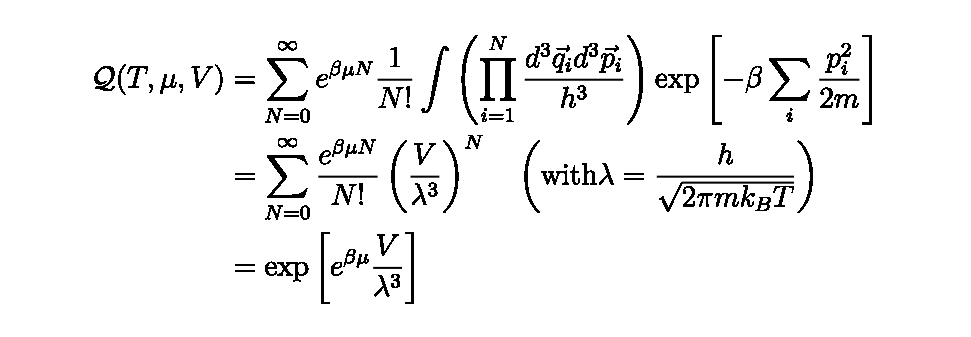

```mathematica
MaTeX["\\begin{aligned}\\mathcal{Q}(T, \\mu, V) & =\\sum_{N=0}^{\\infty} e^{\\beta \\mu N} \\frac{1}{N!} \\int\\left(\\prod_{i=1}^{N} \\frac{d^{3} \\vec{q}_{i} d^{3} \\vec{p}_{i}}{h^{3}}\\right) \\exp \\left[-\\beta \\sum_{i} \\frac{p_{i}^{2}}{2 m}\\right] \\\\& =\\sum_{N=0}^{\\infty} \\frac{e^{\\beta \\mu N}}{N!}\\left(\\frac{V}{\\lambda^{3}}\\right)^{N} \\quad\\left(\\text {with} \\lambda=\\frac{h}{\\sqrt{2 \\pi m k_{B} T}}\\right) \\\\& =\\exp \\left[e^{\\beta \\mu} \\frac{V}{\\lambda^{3}}\\right]\\end{aligned}", Magnification -> 4]
```

```mathematica
(91) -- and the grand potential is
```

Statistical Mechanics
Ramirez (92)

```mathematica
MaTeX["\\mathcal{G}(T, \\mu, V)=-k_{B} T \\ln \\mathcal{Q}=-k_{B} T e^{\\beta \\mu} \\frac{V}{\\lambda^{3}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathcal{G}(T, \\mu, V)=-k_{B} T \\ln \\mathcal{Q}=-k_{B} T e^{\\beta \\mu} \\frac{V}{\\lambda^{3}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

G[T,μ,V]==-k_B T ln Q==-(k_B T e^βμ V)/λ^3

```mathematica
(93) -- But, since $\mathcal{G}=E-T S-\mu N=-P V$, the gas pressure can be obtained directly as
```

Statistical Mechanics
Ramirez (94)

```mathematica
MaTeX["P=-\\frac{\\mathcal{G}}{V}=-\\left.\\frac{\\partial \\mathcal{G}}{\\partial V}\\right|_{\\mu, T}=k_{B} T \\frac{e^{\\beta \\mu}}{\\lambda^{3}}", Magnification -> 4]
```

-Graphics-

(95) -- The particle number and the chemical potential are related by

Statistical Mechanics
Ramirez (96)

```mathematica
MaTeX["N=-\\left.\\frac{\\partial \\mathcal{G}}{\\partial \\mu}\\right|_{T, V}=\\frac{e^{\\beta \\mu} V}{\\lambda^{3}}", Magnification -> 4]
```

-Graphics-

```mathematica
(97) -- In our study of thermodynamics, we can derive a simple yet powerful equation of state by comparing two important equations we've previously discussed. This comparison leads us to the ideal gas law: P = kBTN/V. Here, P is pressure, kB is Boltzmann's constant, T is temperature, N is the number of particles, and V is volume. This equation beautifully connects these fundamental variables, showing how they relate in an ideal gas.

We can also determine the chemical potential, which is crucial for understanding how energy changes as particles are added or removed from the system. This concept helps us bridge thermodynamics with particle behavior at the microscopic level.
```

Statistical Mechanics
Ramirez (98)

```mathematica
MaTeX["\\mu=k_{B} T \\ln \\left(\\lambda^{3} \\frac{N}{V}\\right)=k_{B} T \\ln \\left(\\frac{P \\lambda^{3}}{k_{B} T}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mu=k_{B} T \\ln \\left(\\lambda^{3} \\frac{N}{V}\\right)=k_{B} T \\ln \\left(\\frac{P \\lambda^{3}}{k_{B} T}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

μ==k_B T Log[(λ^3 N)/V]==k_B T Log[(P λ^3)/(k_B T)]

## Reference

https://assets.cambridge.org/97805218/73420/frontmatter/9780521873420_frontmatter.pdf

```mathematica
ThermoLecsDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"ThermoLecs24/"<>ThermoLecsDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear